```mathematica
∫_(0.5x)^x 2/π * r*ArcSin[(x-r)/r]ⅆr
```

0.0872066 x^2

```mathematica
∫_0.8^1 2/π * r*ArcSin[(r-0.8)/r]ⅆr
```

0.0127792

```mathematica
y = (4/(3π)+1/8)x^2+1/(3π)(3ArcSin[1-x]-√(x(2-x))*(1+x))
```

(1/8+4/(3 π)) x^2+(-√((2-x) x) (1+x)+3 ArcSin[1-x])/(3 π)

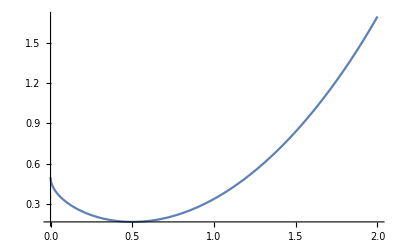

```mathematica
Plot[(4/(3π)+1/8)x^2+1/(3π)*(3ArcSin[1-x]-Sqrt[x(2-x)]*(1+x)), {x, 0, 2}]
```

```mathematica
FindMinValue[(4/(3π)+1/8)x^2+1/(3π)(3ArcSin[1-x]-√(x(2-x))*(1+x)),{{x,0.5}}]
```

0.166186

```mathematica
NumberForm[FindMinValue[(4/(3π)+1/8)x^2+1/(3π)(3ArcSin[1-x]-√(x(2-x))*(1+x)),{{x,0.5}}],16]
```

0.1661864864740086

```mathematica
NumberForm[FindArgMin[(4/(3π)+1/8)x^2+1/(3π)(3ArcSin[1-x]-√(x(2-x))*(1+x)),x],10]
```

{0.501306994}

```mathematica
NumberForm[FindMinValue[(4/(3π)+1/8)x^2+1/(3π)(3ArcSin[1-x]-√(x(2-x))*(1+x)),{{x,0.5}}],10]
```

0.1661864865